```mathematica
f[x_,y_]=Exp[-x^2-y^2]
Grad[f[x,y],{x,y}]
```

ⅇ^(-x^2-y^2)

{-2 ⅇ^(-x^2-y^2) x,-2 ⅇ^(-x^2-y^2) y}

```mathematica
Solve[{-2 ⅇ^(-x^2-y^2) x==0,-2 ⅇ^(-x^2-y^2) y==0},{x,y}]
```

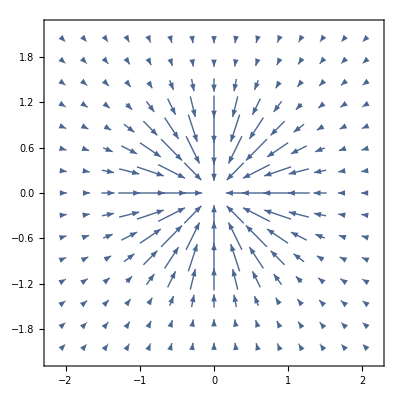

```mathematica
VectorPlot[Evaluate@Grad[f[x,y],{x,y}],{x,-2,2},{y,-2,2}]
```

```mathematica
grad=FullSimplify[Grad[Abs[-1/(x^2+y^2)],{x,y}],{x,y}∈Reals]
```

{-(2 x Sign[x^2+y^2])/((x^2+y^2)^2),-(2 y Sign[x^2+y^2])/((x^2+y^2)^2)}

```mathematica
Plot3D[Abs[grad],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Total[Abs[grad]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

30

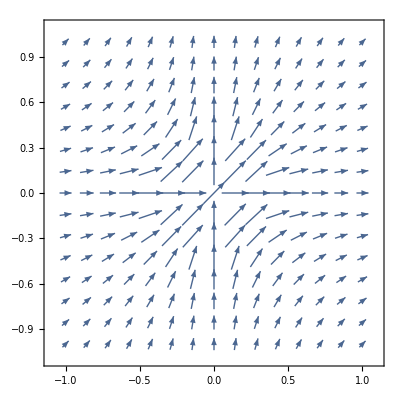

```mathematica
topval=30
VectorPlot[Map[Min[topval,#]&,Abs[grad]],{x,-1,1},{y,-1,1},VectorScale->{Automatic,Automatic,Function[If[#5>50,None,#5^.3]]}]
```

Left off: figure out why it wants to be decreasing in +x,+y even though the graphs don’t show it doing that

```mathematica
Abs[grad]
```

{2 Abs[(x Sign[x^2+y^2])/((x^2+y^2)^2)],2 Abs[(y Sign[x^2+y^2])/((x^2+y^2)^2)]}

```mathematica
Map[(1+#)&,grad]
```

{1-(2 x Sign[x^2+y^2])/((x^2+y^2)^2),1-(2 y Sign[x^2+y^2])/((x^2+y^2)^2)}

```mathematica
Map[Min[topval,#]&,Abs[grad]]
```

{Min[1000000,2 Abs[(x Sign[x^2+y^2])/((x^2+y^2)^2)]],Min[1000000,2 Abs[(y Sign[x^2+y^2])/((x^2+y^2)^2)]]}

```mathematica
-(2 x Sign[x^2+y^2])/((x^2+y^2)^2)/.{x->2,y->2}
```

-1/16